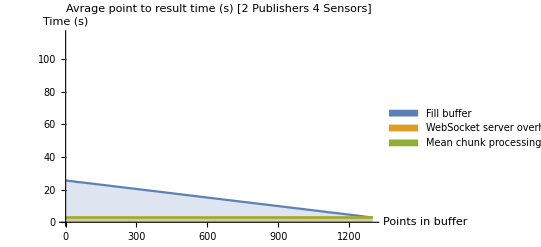

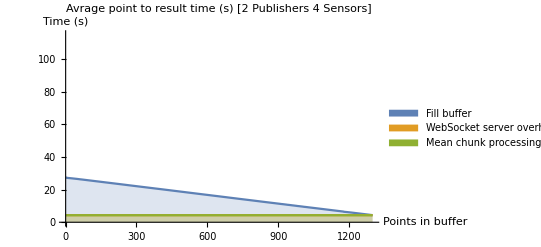

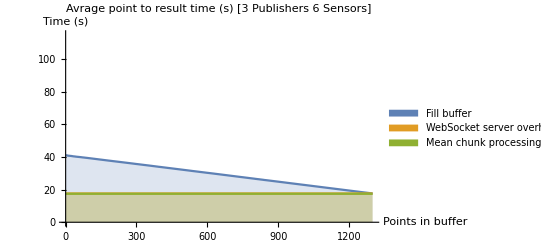

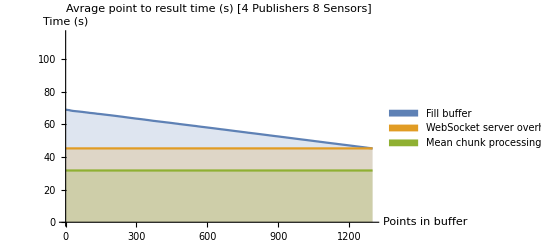

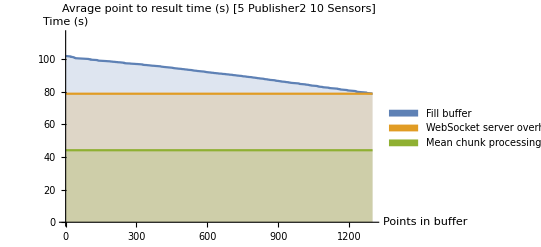

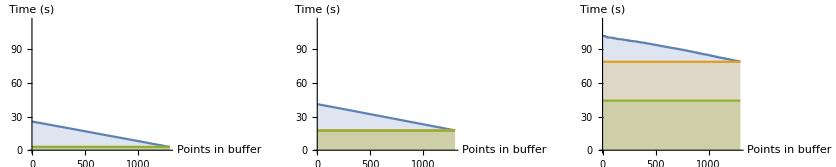

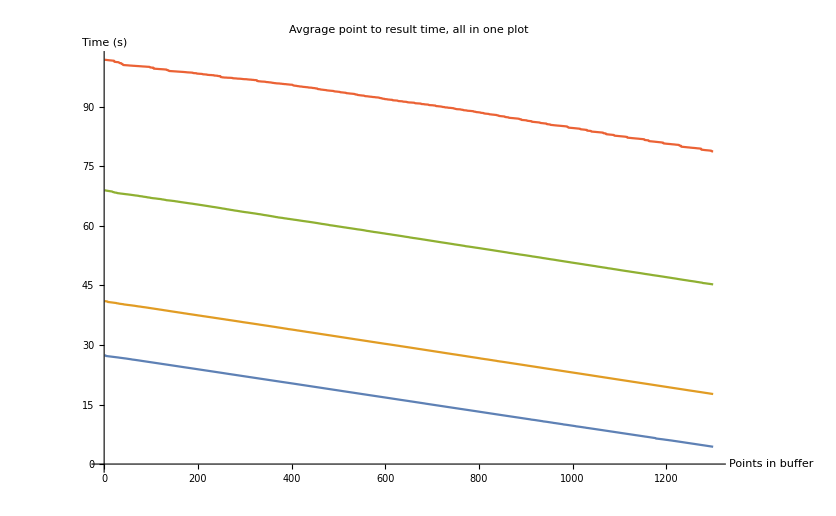

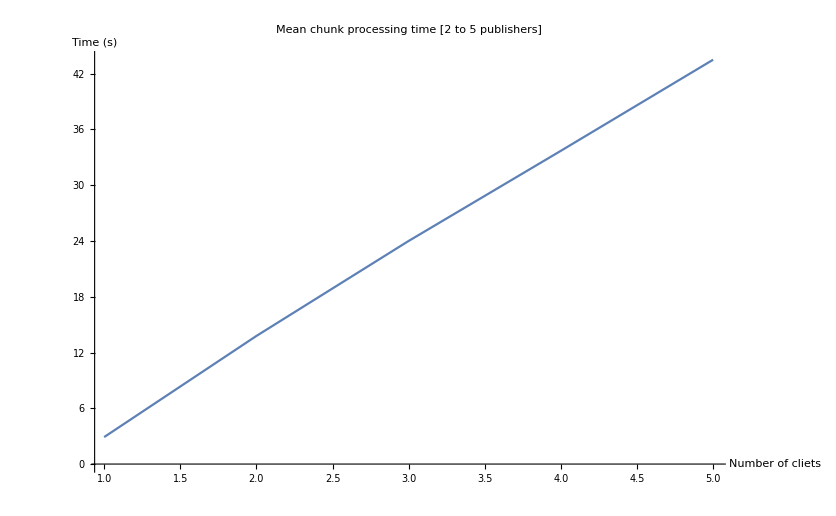

```mathematica
data00 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330025.json"}]];
data0 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330026.json"}]];
data1 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330027.json"}]];
data2 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330028.json"}]];
data3 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330029.json"}]];




(*Static lines to show realtion with mean chunk procesisng time.*)
data00meanstatic = {{1,2.89}, {1300,2.89}};
data00overhead = {{1,Last[data00]},{1300,Last[data00]} };

data0meanstatic = {{1,4.3}, {1300,4.3}};
data0overhead = {{1,Last[data0]},{1300,Last[data0]} };

data1meanstatic = {{1,17.45}, {1300,17.45}};
data1overhead = {{1,Last[data1]},{1300,Last[data1]} };

data2meanstatic = {{1,31.71}, {1300,31.71}};
data2overhead = {{1,Last[data2]},{1300,Last[data2]} };

data3meanstatic = {{1,44.12}, {1300,44.12}};
data3overhead = {{1,Last[data3]},{1300,Last[data3]} };

meanchunkprocessingtime = {{1,2.9},{2,13.78},{3,24}, {4,33.7},{5,43.5}};

(*Data plots separated with legends and caption*)
ListPlot[{data00,  data00overhead,data00meanstatic}, Joined->True, PlotLabel->"Avrage point to result time (s)  [2 Publishers 4 Sensors]", AxesLabel->{"Points in buffer","Time (s)"}, Filling->Axis, PlotRange->{{0,1300},{0,115}}, PlotLegends->SwatchLegend[{"Fill buffer","WebSocket server overhead", "Mean chunk processing time"}]]

ListPlot[{data0,  data0overhead,data0meanstatic}, Joined->True, PlotLabel->"Avrage point to result time (s)  [2 Publishers 4 Sensors]", AxesLabel->{"Points in buffer","Time (s)"}, Filling->Axis, PlotRange->{{0,1300},{0,115}}, PlotLegends->SwatchLegend[{"Fill buffer","WebSocket server overhead", "Mean chunk processing time"}]]


ListPlot[{data1, data1overhead,data1meanstatic}, Joined->True, PlotLabel->"Avrage point to result time (s)  [3 Publishers 6 Sensors]", AxesLabel->{"Points in buffer","Time (s)"}, Filling->Axis,PlotRange->{{0,1300},{0,115}},PlotLegends->SwatchLegend[{"Fill buffer","WebSocket server overhead", "Mean chunk processing time"}]]


ListPlot[{data2, data2overhead,data2meanstatic}, Joined->True, PlotLabel->"Avrage point to result time (s)  [4 Publishers 8 Sensors]", AxesLabel->{"Points in buffer","Time (s)"}, Filling->Axis,PlotRange->{{0,1300},{0,115}},PlotLegends->SwatchLegend[{"Fill buffer","WebSocket server overhead", "Mean chunk processing time"}]]


ListPlot[{data3,data3overhead,data3meanstatic}, Joined->True, PlotLabel->"Avrage point to result time (s)  [5 Publisher2 10 Sensors]", AxesLabel->{"Points in buffer","Time (s)"},Filling->Axis,PlotRange->{{0,1300},{0,115}},PlotLegends->SwatchLegend[{"Fill buffer","WebSocket server overhead", "Mean chunk processing time"}]]

(*Data plots on a row*)
a = ListPlot[{data00,  data00overhead,data00meanstatic}, Joined->True,AxesLabel->{"Points in buffer","Time (s)"}, Filling->Axis, PlotRange->{{0,1300},{0,115}}];
b = ListPlot[{data1, data1overhead,data1meanstatic}, Joined->True, AxesLabel->{"Points in buffer","Time (s)"}, Filling->Axis,PlotRange->{{0,1300},{0,115}}];
c = ListPlot[{data3,data3overhead,data3meanstatic}, Joined->True,AxesLabel->{"Points in buffer","Time (s)"},Filling->Axis,PlotRange->{{0,1300},{0,115}}];
GraphicsRow[{a,b,c}]


ListPlot[{data0,data1, data2, data3}, Joined->True, PlotLabel->"Avgrage point to result time, all in one plot", AxesLabel->{"Points in buffer","Time (s)"}]
ListPlot[meanchunkprocessingtime, Joined->True, PlotLabel->"Mean chunk processing time [2 to 5 publishers]", AxesLabel->{"Number of cliets","Time (s)"}]
```